# Fit parabolico dei dati Parabolic Regression of Data

## Metodo dei Minimi Quadrati Method of the Least Squares

# Istruzioni Instructions

Il presente foglio di calcolo di Mathematica permette di calcolare un fit parabolico dei dati inseriti da un file .dat contenente tre colonne in cui siano inseriti, nell’ordine, ascisse, ordinate, errore sulle ordinate.
Il file di input può contenere anche un’eventuale riga di intestazione dei dati, che verrà automaticamente ignorata dal programma.
Dopo aver inserito i dati nella sezione “Input dei dati” è sufficiente dare il comando “Evaluate Notebook” dal menù “Evaluation”. Il risultato dell’analisi viene salvato in file all’interno della cartella “Documenti”, recanti il nome dell’analisi (viene creata una cartella dal nome dell’esperienza). E’ possibile far eseguire più di un’analisi all’interno della stessa esperienza, posto di cambiare il nome del fit relativo (cioè il nome della sottocartella).

Per info:
Riccardo Finotello
riccardo.finotello@edu.unito.it

This Mathematica notebook provides a method to perform a quadratic regression regression of data in an external file (.dat), with four columns stating, in this order, ascissae, ordinata, error in the ascissae (even if none) and error in ordinata.
The input file may contain a title line, which will be automatically ignored. After inputting data in the first section, a simple “Evaluate notebook” should do the trick (Go to the “Evaluation” menu). The result is then stored in a separate file, inside the “Documents” directory, with analysis name (a subdirectory will be created). It is possible to perform multiple analysis of the same experience (remember to change the name of the regression).

Info:
Riccardo Finotello
riccardo.finotello@edu.unito.it

# Input dei dati Data input

```mathematica
Clear["Global`*"] (* restting notebook *)
Needs["ErrorBarPlots`"](* error bars package *)
```

```mathematica
NomeEsperienza="EffettoHall";(* name of the main directory: avoid spaces *)
NomeFit="1200mA";(* name of the subdirectory: avoid spaces *)
InputFile="Desktop\\1200mA.dat";(* insert path to file: \\ or / to separate *)
EtichettaAscissa="I" ; (* ascissae label *)
UnitàMisuraAscissa="mA";(* unit of measure for the ascissae: insert _ or Blank[] if not needed *)
EtichettaOrdinata="V"; (* ordinata label *)
UnitàMisuraOrdinata="mV";(* unit of measure for the ordinata: insert _ or Blank[] if not needed *)
```

# Analisi dei dati

### Input del file indicato Inputting the file

```mathematica
inputData=Import[InputFile,"Data"];
Grid[inputData]
```

-8.04 | -14.31 | 0.02 | 0.02
-6.9 | -12.35 | 0.02 | 0.02
-6. | -10.84 | 0.02 | 0.02
-5.56 | -9.93 | 0.02 | 0.02
-5.03 | -8.95 | 0.02 | 0.02
-3.85 | -6.85 | 0.02 | 0.02
-2.9 | -5.17 | 0.02 | 0.02
-1.91 | -3.41 | 0.02 | 0.02
-0.92 | -1.71 | 0.02 | 0.02
-0.47 | -0.85 | 0.02 | 0.02
0. | 0. | 0.02 | 0.02
0.48 | 0.79 | 0.02 | 0.02
0.9 | 1.53 | 0.02 | 0.02
1.96 | 3.45 | 0.02 | 0.02
2.89 | 5.24 | 0.02 | 0.02
3.93 | 7.13 | 0.02 | 0.02
5.03 | 8.98 | 0.02 | 0.02
5.5 | 9.96 | 0.02 | 0.02
6.05 | 10.87 | 0.02 | 0.02
7.01 | 12.65 | 0.02 | 0.02
8.01 | 14.29 | 0.02 | 0.02

### Costruzione liste di ascisse, ordinate ed errori Ascissae and ordinata lists (with errors)

```mathematica
If[StringQ[inputData[[1,1]]],ascissa=Drop[Flatten[inputData[[All,1]]],1],ascissa=Flatten[inputData[[All,1]]]];
If[StringQ[inputData[[1,2]]],ordinata=Drop[Flatten[inputData[[All,2]]],1],ordinata=Flatten[inputData[[All,2]]]];
If[StringQ[inputData[[1,3]]],sigmaAscissa=Drop[Flatten[inputData[[All,3]]],1],sigmaAscissa=Flatten[inputData[[All,3]]]];
If[StringQ[inputData[[1,4]]],sigmaOrdinata=Drop[Flatten[inputData[[All,4]]],1],sigmaOrdinata=Flatten[inputData[[All,4]]]];
Lungh=Length[ascissa];
```

```mathematica
TopLimit=50;
If[Lungh≤TopLimit,Print["x = ",ascissa],"Lists are too long to be shown"]
If[Lungh≤TopLimit,Print["y = ",ordinata],"Lists are too long to be shown"]
If[Lungh≤TopLimit,Print["σ_x = ",sigmaAscissa],"Lists are too long to be shown"]
If[Lungh≤TopLimit,Print["σ_y = ",sigmaOrdinata],"Lists are too long to be shown"]
```

x = {-8.04,-6.9,-6.,-5.56,-5.03,-3.85,-2.9,-1.91,-0.92,-0.47,0.,0.48,0.9,1.96,2.89,3.93,5.03,5.5,6.05,7.01,8.01}

y = {-14.31,-12.35,-10.84,-9.93,-8.95,-6.85,-5.17,-3.41,-1.71,-0.85,0.,0.79,1.53,3.45,5.24,7.13,8.98,9.96,10.87,12.65,14.29}

σ_x = {0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02}

σ_y = {0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02}

### Controllo dei dati Checking the data

```mathematica
If[Lungh==Length[ordinata]&&Lungh==Length[sigmaAscissa]&&Lungh==Length[sigmaOrdinata],"Lists are consistents","Error: check the input"]
```

Le liste sono consistenti

### Metodo dei Minimi Quadrati (Esp1 - Prof. Balestra) Method of the Least Squares

```mathematica
matD={{Sum[1/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[ascissa[[i]]/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[(ascissa[[i]])^2/(sigmaOrdinata[[i]])^2,{i,Lungh}]},{Sum[ascissa[[i]]/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[(ascissa[[i]])^2/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[(ascissa[[i]])^3/(sigmaOrdinata[[i]])^2,{i,Lungh}]},{Sum[(ascissa[[i]])^2/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[(ascissa[[i]])^3/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[(ascissa[[i]])^4/(sigmaOrdinata[[i]])^2,{i,Lungh}]}}  
matDinver=Inverse[matD];
matB ={Sum[ordinata[[i]]/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[(ascissa[[i]]*ordinata[[i]])/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[((ascissa[[i]])^2*ordinata[[i]])/(sigmaOrdinata[[i]])^2,{i,Lungh}]};
matA = matDinver. matB;
Print["D = ",MatrixForm[matD]]
Print["D^-1 = ",MatrixForm[matDinver]]
Print["B = ",MatrixForm[matB]]
Print["A = ",MatrixForm[matA]]
```

{{4651.55,4681.5,8.96152×10^7},{4681.5,8.96152×10^7,1.64062×10^8},{8.96152×10^7,1.64062×10^8,3.71457×10^12}}

D = (4651.55 | 4681.5 | 8.96152×10^7
4681.5 | 8.96152×10^7 | 1.64062×10^8
8.96152×10^7 | 1.64062×10^8 | 3.71457×10^12)

D^-1 = (0.000401679 | -3.24291×10^-9 | -9.69049×10^-9
-3.24291×10^-9 | 1.11598×10^-8 | -4.1466×10^-13
-9.69049×10^-9 | -4.1466×10^-13 | 5.03015×10^-13)

B = (241136.
243933.
4.67399×10^9)

A = (51.5651
2.14228×10^-6
0.0000142609)

### Creazione dei grafici Plots creation

```mathematica
dati=Table[{ascissa[[i]],ordinata[[i]]},{i,Lungh}];
If[Lungh≤TopLimit,Grid[dati],"Grid is too long to be shown"]
```

-262.822 | 52.5337
-230.022 | 52.3256
-176.477 | 52.0318
-159.988 | 51.9461
-139.776 | 51.8482
-123.11 | 51.787
-104.671 | 51.7136
-86.2316 | 51.6646
-69.5654 | 51.6157
-52.8992 | 51.5912
-32.5097 | 51.5545
-17.7938 | 51.5545
1 | 51.5912
19.7938 | 51.5789
36.46 | 51.5789
56.8495 | 51.6157
71.7427 | 51.6401
90.3592 | 51.6769
107.025 | 51.7258
123.692 | 51.787
144.258 | 51.8727
158.974 | 51.9339
175.641 | 52.0073
230.958 | 52.3501
264.468 | 52.5337

```mathematica
err=Table[{dati[[i]],ErrorBar[sigmaOrdinata[[i]]]},{i,Lungh}];
If[Lungh≤TopLimit,Grid[err],"Grid is too long to be shown"]
```

{-262.822,52.5337} | ErrorBar[0.0740467]
{-230.022,52.3256} | ErrorBar[0.0738257]
{-176.477,52.0318} | ErrorBar[0.0735139]
{-159.988,51.9461} | ErrorBar[0.0734231]
{-139.776,51.8482} | ErrorBar[0.0733193]
{-123.11,51.787} | ErrorBar[0.0732545]
{-104.671,51.7136} | ErrorBar[0.0731768]
{-86.2316,51.6646} | ErrorBar[0.0731249]
{-69.5654,51.6157} | ErrorBar[0.0730731]
{-52.8992,51.5912} | ErrorBar[0.0730472]
{-32.5097,51.5545} | ErrorBar[0.0730084]
{-17.7938,51.5545} | ErrorBar[0.0730084]
{1,51.5912} | ErrorBar[0.0730472]
{19.7938,51.5789} | ErrorBar[0.0730343]
{36.46,51.5789} | ErrorBar[0.0730343]
{56.8495,51.6157} | ErrorBar[0.0730731]
{71.7427,51.6401} | ErrorBar[0.073099]
{90.3592,51.6769} | ErrorBar[0.0731379]
{107.025,51.7258} | ErrorBar[0.0731897]
{123.692,51.787} | ErrorBar[0.0732545]
{144.258,51.8727} | ErrorBar[0.0733453]
{158.974,51.9339} | ErrorBar[0.0734101]
{175.641,52.0073} | ErrorBar[0.073488]
{230.958,52.3501} | ErrorBar[0.0738516]
{264.468,52.5337} | ErrorBar[0.0740467]

```mathematica
If[StringQ[UnitàMisuraAscissa],AscissaLabel=EtichettaAscissa<>" ["<>UnitàMisuraAscissa<>"]",AscissaLabel=EtichettaAscissa];
If[StringQ[UnitàMisuraOrdinata],OrdinataLabel=EtichettaOrdinata<>" ["<>UnitàMisuraOrdinata<>"]",OrdinataLabel=EtichettaOrdinata];
```

### Grafici e parametri del primo fit First regression plots

#### Grafico dei punti sperimentali Experimental data

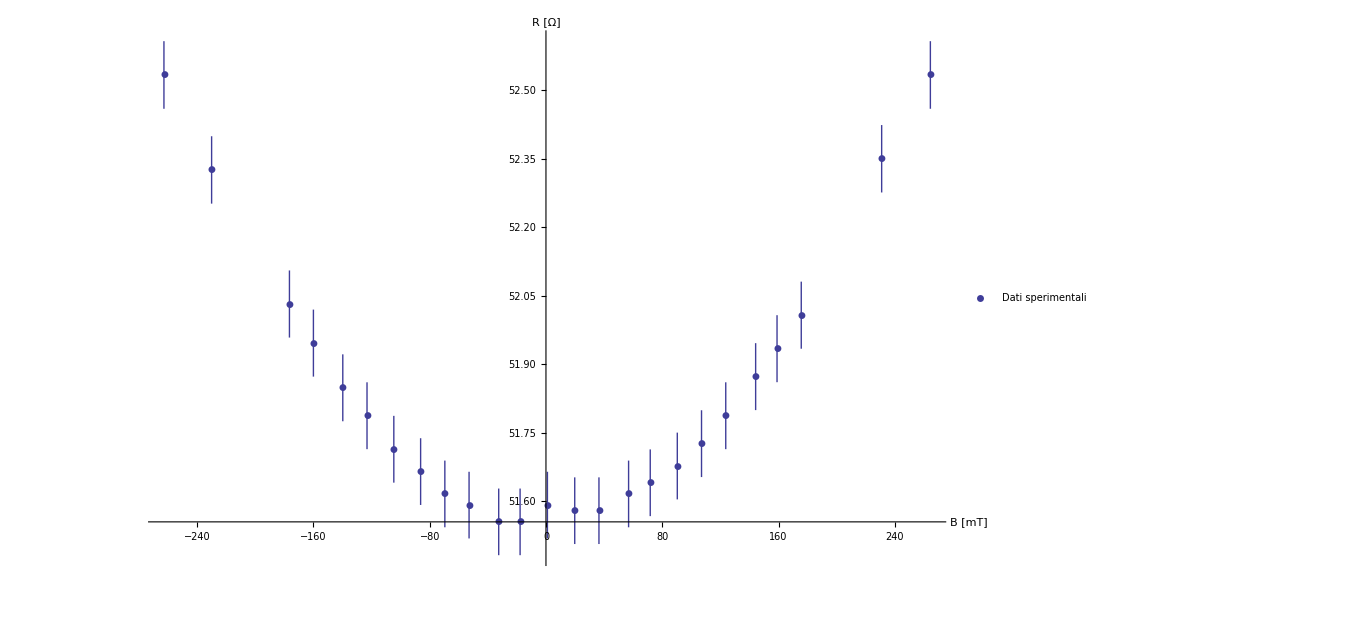

```mathematica
Grafico=ErrorListPlot[err,PlotRange->All,AxesLabel->{AscissaLabel,OrdinataLabel},LabelStyle->Directive[Black,Bold,Large],ImageSize->1000,PlotMarkers->Automatic,PlotLegends->{"Experimental data"}]
```

#### Parametri del fit lineare con il metodo dei minimi quadrati Least Squares parameters

```mathematica
a=matA[[1]];
siga=Sqrt[matDinver[[1,1]]];
b=matA[[2]];
sigb=Sqrt[matDinver[[2,2]]];
c=matA[[3]];
sigc=Sqrt[matDinver[[3,3]]];
f[x_]:=a+b*x+c*x*x;
Print["y = f(x) = a + bx + cx^2"]
Print["a = (",a," ± ",siga,")",If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata,""]]
Print["b = (",b," ± ",sigb,")",If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata<>If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa^-1,""],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa^-1,""]]]
Print["c = (",c," ± ",sigc,")",If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata<>If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa^-2,""],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa^-2,""]]]
```

Parabola y = f(x) = a + bx + cx^2

a = (51.5651 ± 0.0200419)Ω

StringJoin::string: String expected at position 2 in "\[CapitalOmega]" <> 1/"mT".

b = (2.14228×10^-6 ± 0.00010564)Ω<>1/mT

StringJoin::string: String expected at position 2 in "\[CapitalOmega]" <> 1/"mT"^2.

c = (0.0000142609 ± 7.09235×10^-7)Ω<>1/mT^2

#### Grafico della parabola di fit Quadratic regression

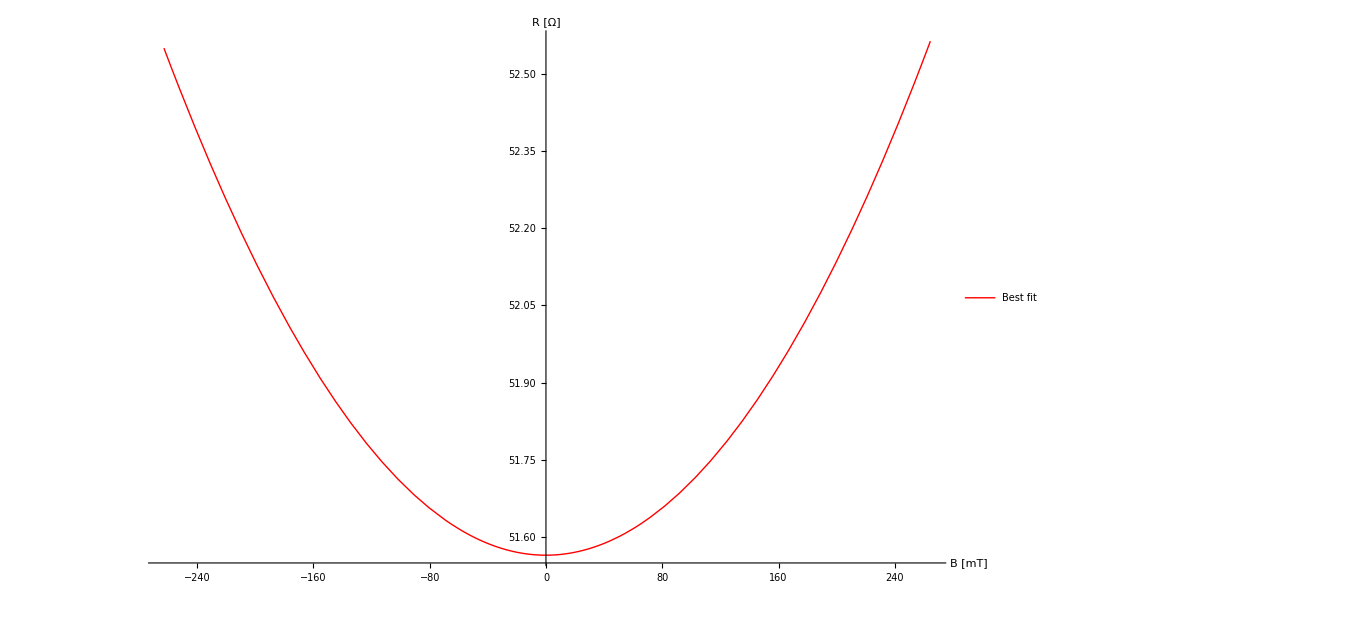

```mathematica
GraficoParabola=Plot[f[x],{x,First[ascissa],Last[ascissa]},PlotRange->All,ImageSize->1000,AxesLabel->{AscissaLabel,OrdinataLabel},LabelStyle->Directive[Black,Bold,Large],PlotStyle->Red,PlotLegends->{"Best fit"}]
```

#### Grafico cumulativo (dati e parabola) Experimental data and regression

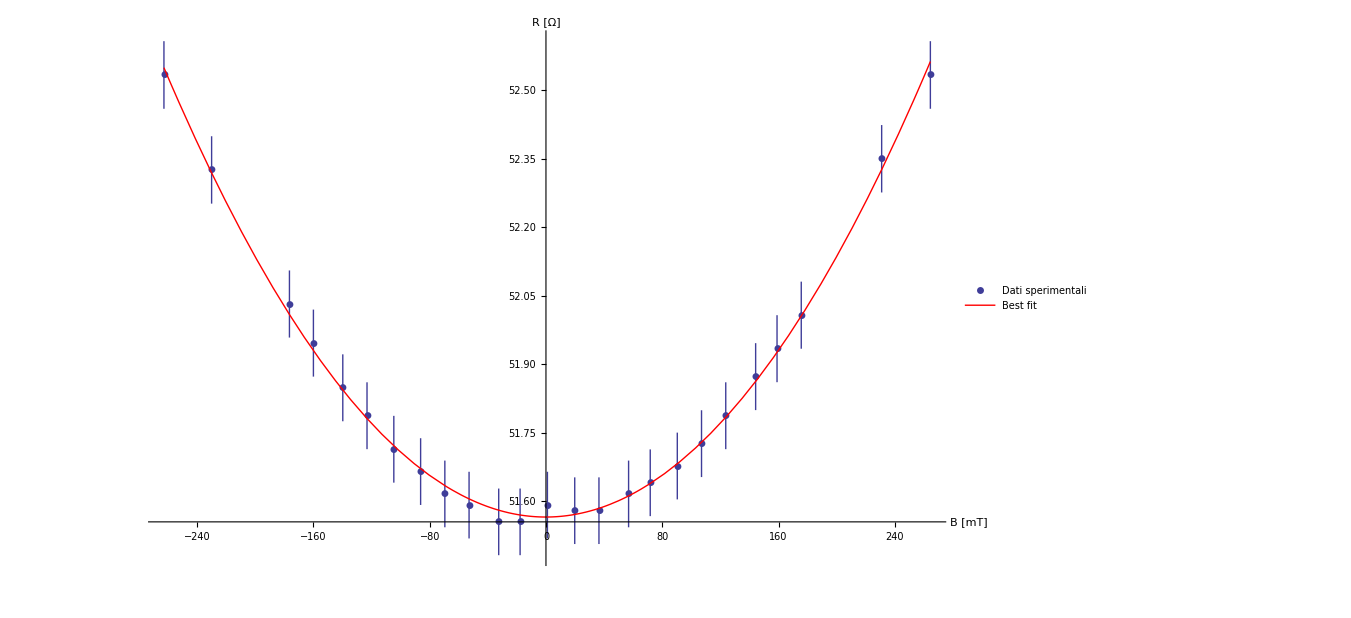

```mathematica
GraficoTot=Show[Grafico,GraficoParabola]
```

#### Parametri del Chi Quadro Chi Square

```mathematica
chi2=Sum[(f[ascissa[[i]]]-ordinata[[i]])^2/sigmaOrdinata[[i]]^2,{i,Lungh}];
sy=Sqrt[Sum[(f[ascissa[[i]]]-ordinata[[i]])^2/(Lungh-3),{i,Lungh}]];
Print["Linear correlation coefficient : ρ = ",Correlation[ascissa,ordinata]] (* compare to a linear distribution *)
Print["χ^2 = ",chi2]
Print["Degrees of freedom: dof = ",Lungh-3]
Print["A posteriori error on ordinata: σ_y = ",sy,If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata,""]]
```

Coefficiente di correlazione lineare: ρ = 0.00649328

χ^2 = 0.946815

Gradi di libertà del sistema: dof = 22

Eventuale errore a posteriori sulle ordinate: σ_y = 0.0152351Ω

# Export su file

```mathematica
dir=$UserDocumentsDirectory<>"\\"<>NomeEsperienza<>"\\"<>NomeFit;
CreateDirectory[dir];
```

CreateDirectory::filex: "C:\\Users\\ricca_000\\Documents\\EffettoHall\\MagnetoresistenzaTotale\\" already exists.

```mathematica
If[DirectoryQ[dir<>"\\Analisi"],Analisi=SetDirectory[dir<>"\\Analisi"],Analisi=CreateDirectory[dir<>"\\Analisi"]];
SetDirectory[dir];
Print["File will be created in: ",dir]
```

I file verranno inseriti nelle cartelle corrispondenti al seguente indirizzo: C:\Users\ricca_000\Documents\EffettoHall\MagnetoresistenzaTotale

#### Export dei contenuti dell’analisi

```mathematica
outputAnalisi={{,"Data analysis (errors on ordinata)",},{,,},{,"Chi Square parameters (y = a + bx)",},{"Parameter","Error","Units"},{"a = ",a,siga,If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata,""]},{"b = ",b,sigb,If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata<>If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa<>"^(-1)",""],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa<>"^(-1)",""]]},{"c = ",c,sigc,If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata<>If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa<>"^(-2)",""],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa<>"^(-2)",""]]},{,,},{,"Linear correlation coefficient",},{"r = ",Correlation[ascissa,ordinata],},{,,},{,"Chi Square",},{"chi = ",chi2,},{,,},{,"A posteriori error",},{"sigma = ",sy,},{,,},{,"Degrees of freedom",},{"dof = ",Lungh-3,}};
Export[file1=Analisi<>"\\AnalisiDati.xls",outputAnalisi];
Export[graph11=Analisi<>"\\GraficoExp.png",Grafico];
Export[graph21=Analisi<>"\\GraficoParabola.png",GraficoParabola];
Export[graph31=Analisi<>"\\GraficoSovrapposto.png",GraficoTot];
SetDirectory[dir];
If[FileExistsQ[file1],"File saved in: "<>file1,"Error: check parameters"]
If[FileExistsQ[graph11],"File saved in: "<>graph11,"Error: check parameters"]
If[FileExistsQ[graph21],"File saved in: "<>graph21,"Error: check parameters"]
If[FileExistsQ[graph31],"File saved in: "<>graph31,"Error: check parameters"]
```

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\MagnetoresistenzaTotale\Analisi\AnalisiDati.xls

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\MagnetoresistenzaTotale\Analisi\GraficoExp.png

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\MagnetoresistenzaTotale\Analisi\GraficoParabola.png

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\MagnetoresistenzaTotale\Analisi\GraficoSovrapposto.png